должно быть уравнение:

-23.+24.5 x

наше уравнение

-23.4894+24.7937 x

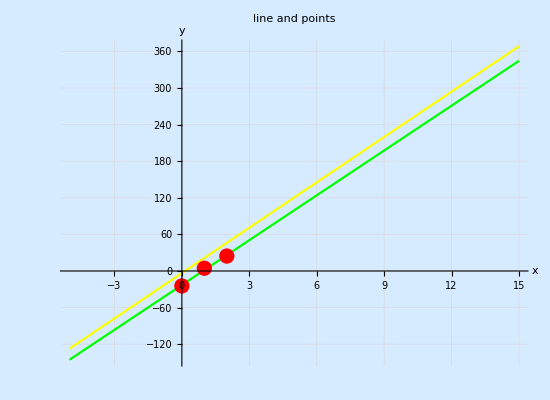

```mathematica
points=ReadList["/Users/konov_mark/C++/valed/line_point/points.txt",Real];
(*linepoints=ReadList["/Users/konov_mark/C++/valed/line_point/line_points.txt",Real];*)
linecoefs=ReadList["/Users/konov_mark/C++/valed/line_point/line_coefs.txt",Real];

partpoints=Partition[points,2];
(*partline=Partition[linepoints,2];*)

wline=LinearModelFit[partpoints,x,x];
Print["должно быть уравнение:"]
Normal[wline]
Print["наше уравнение"]
-linecoefs[[1]]*x/linecoefs[[2]]+linecoefs[[3]]/linecoefs[[2]]

Show[
	{
		Graphics[
			{
			(*{Blue, InfiniteLine[partline]}*)
			(*,
			{Table[
				{Red, PointSize[0.02],Point[{partpoints[[i]]}]}
				,
				{i,1,Length[partpoints]}]}*)
			}
			,
			Axes->True, 
			AxesOrigin->{0,0},
			ImageSize->{550,400},
			AspectRatio->Full, 
			Background->RGBColor[0.84,0.92,1.],
			AxesLabel->{HoldForm[x],HoldForm[y]},
			PlotLabel->HoldForm[line and points],
			LabelStyle->{FontFamily->"Avenir Next",14,GrayLevel[0],Bold},
			GridLines->Automatic, 
			GridLinesStyle->Directive[Red,Dotted]]
		,
		Plot[{wline[x]}
			,
			{x,-5,15},
			PlotStyle->Green]
		,
		Plot[{y=-linecoefs[[1]]*x/linecoefs[[2]]+linecoefs[[3]]/linecoefs[[2]]+20}
			,
			{x,-5,15},
			PlotStyle->Yellow]
		,
		ListPlot[partpoints
			,
			PlotStyle->{Red,PointSize[0.02]}]
	}
]
```